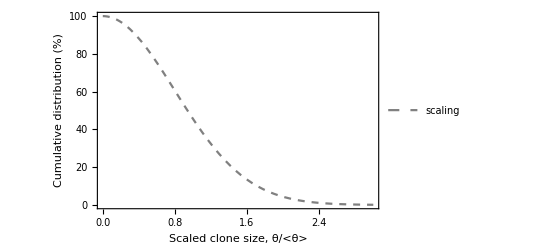

```mathematica
g1=Plot[100Exp[-Pi x^2/4],{x,0,3},FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->{Dashed,Gray},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled clone size, θ/<θ>","Cumulative distribution (%)"},PlotLegends->{Style["scaling",FontFamily->"Myriad Pro",FontSize->16]}]
```

```mathematica
!modify datafile below to index current directory!
```

```mathematica
datafile="/Users/benjaminsimons/Library/Mobile Documents/com~apple~CloudDocs/biology/intestine/red2/red_fort/for_paper/source_fig2ab/data_for_fig2ab.xlsx";dat4=Import[datafile,{"Data",1,Range[21],{1,2}}];d4={#1,#2}&@@@dat4;dat7=Import[datafile,{"Data",1,Range[4,24],{4,5}}];d7={#1,#2}&@@@dat7;dat14=Import[datafile,{"Data",1,Range[4,24],{7,8}}];d14={#1,#2}&@@@dat14;dat21=Import[datafile,{"Data",1,Range[4,24],{10,11}}];d21={#1,#2}&@@@dat21;
```

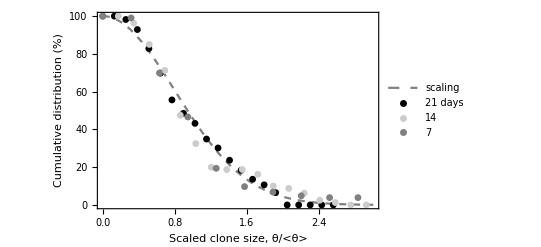

```mathematica
p4=ListPlot[d4,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->GrayLevel[0.9],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["4",FontFamily->"Myriad Pro",FontSize->16]}];p7=ListPlot[d7,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->GrayLevel[0.5],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["7",FontFamily->"Myriad Pro",FontSize->16]}];p14=ListPlot[d14,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->GrayLevel[0.8],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["14",FontFamily->"Myriad Pro",FontSize->16]}];p21=ListPlot[d21,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled clone size, θ/<θ>","Cumulative distribution (%)"},PlotLegends->{Style["21 days",FontFamily->"Myriad Pro",FontSize->16]}];Show[g1,p21,p14,p7]
```

```mathematica
dat7=Import[datafile,{"Data",1,Range[4,24],{14,15}}];nk7={#1,#2}&@@@dat7;dat14=Import[datafile,{"Data",1,Range[4,24],{17,18}}];nk14={#1,#2}&@@@dat14;dat21=Import[datafile,{"Data",1,Range[4,24],{20,21}}];nk21={#1,#2}&@@@dat21;
```

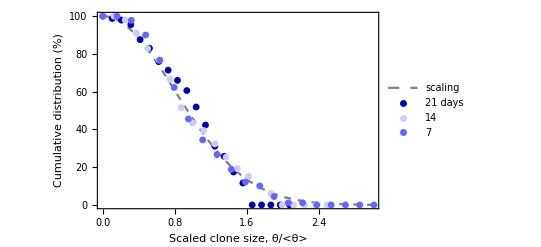

```mathematica
pk7=ListPlot[nk7,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Blue,0.4],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["7",FontFamily->"Myriad Pro",FontSize->16]}];pk14=ListPlot[nk14,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Blue,0.8],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["14",FontFamily->"Myriad Pro",FontSize->16]}];pk21=ListPlot[nk21,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Darker[Blue,0.3],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled clone size, θ/<θ>","Cumulative distribution (%)"},PlotLegends->{Style["21 days",FontFamily->"Myriad Pro",FontSize->16]}];Show[g1,pk21,pk14,pk7]
```

```mathematica
dat7=Import[datafile,{"Data",1,Range[4,24],{24,25}}];np7={#1,#2}&@@@dat7;dat14=Import[datafile,{"Data",1,Range[4,24],{27,28}}];np14={#1,#2}&@@@dat14;dat21=Import[datafile,{"Data",1,Range[4,24],{30,31}}];np21={#1,#2}&@@@dat21;
```

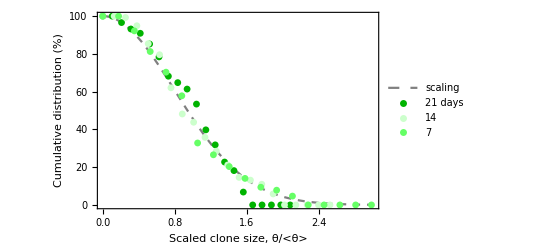

```mathematica
pp7=ListPlot[np7,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Green,0.4],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["7",FontFamily->"Myriad Pro",FontSize->16]}];pp14=ListPlot[np14,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Green,0.8],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["14",FontFamily->"Myriad Pro",FontSize->16]}];pp21=ListPlot[np21,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Darker[Green,0.3],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled clone size, θ/<θ>","Cumulative distribution (%)"},PlotLegends->{Style["21 days",FontFamily->"Myriad Pro",FontSize->16]}];Show[g1,pp21,pp14,pp7]
```

```mathematica
dat7=Import[datafile,{"Data",1,Range[4,24],{34,35}}];nn7={#1,#2}&@@@dat7;dat14=Import[datafile,{"Data",1,Range[4,24],{37,38}}];nn14={#1,#2}&@@@dat14;dat21=Import[datafile,{"Data",1,Range[4,24],{40,41}}];nn21={#1,#2}&@@@dat21;
```

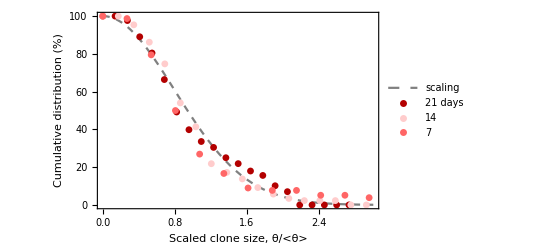

```mathematica
pn7=ListPlot[nn7,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Red,0.4],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["7",FontFamily->"Myriad Pro",FontSize->16]}];pn14=ListPlot[nn14,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Lighter[Red,0.8],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},PlotLegends->{Style["14",FontFamily->"Myriad Pro",FontSize->16]}];pn21=ListPlot[nn21,FrameStyle->{Black,Black,Black,Black},PlotRange->{0,100},Frame->True,PlotStyle->Darker[Red,0.3],PlotMarkers->{Automatic,7},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled clone size, θ/<θ>","Cumulative distribution (%)"},PlotLegends->{Style["21 days",FontFamily->"Myriad Pro",FontSize->16]}];Show[g1,pn21,pn14,pn7]
```

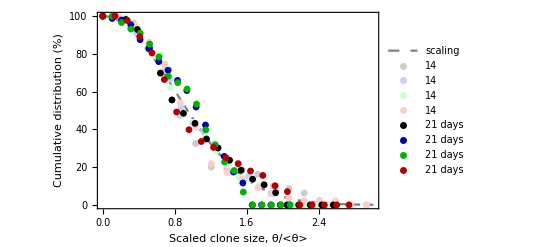

```mathematica
Show[g1,p14,pk14,pp14,pn14,p21,pk21,pp21,pn21]
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
tdelay=2;model=a (x-tdelay)^(1/2)
```

a √(-2+x)

```mathematica
{cnf1,cnf2,cnf3}={71.55465621,130.895455,176.0403466};{cnfer1,cnfer2,cnfer3}={7.050489775,14.63455677,13.54156513};
```

```mathematica
avcnf={{7,cnf1/360},{14,cnf2/360},{21,cnf3/360}}
```

{{7,0.198763},{14,0.363598},{21,0.489001}}

```mathematica
nlmcnf=NonlinearModelFit[avcnf,model,a,x]
```

FittedModel[0.106542 √(-2+x)]

```mathematica
cnf=0.1065415365190704 /Sqrt[Pi];cnfer=nlmcnf["ParameterErrors"]/Sqrt[Pi]
```

{0.00311367}

```mathematica
avcnfer={{{7,cnf1/360},ErrorBar[cnfer1/360]},{{14,cnf2/360},ErrorBar[cnfer2/360]},{{21,cnf3/360},ErrorBar[cnfer3/360]}};
```

```mathematica
savcnfer={{{(7-tdelay)cnf^2,cnf1/360},ErrorBar[cnfer1/360]},{{(14-tdelay)cnf^2,cnf2/360},ErrorBar[cnfer2/360]},{{(21-tdelay)cnf^2,cnf3/360},ErrorBar[cnfer3/360]}};
```

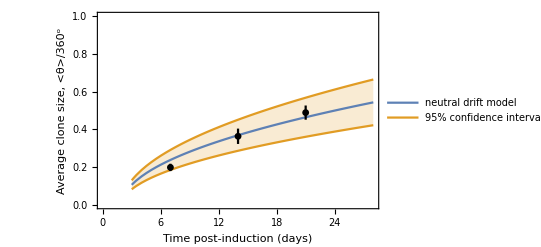

```mathematica
bands95[x_]=nlmcnf["MeanPredictionBands",ConfidenceLevel->.95];
Show[Plot[{nlmcnf[x],bands95[x]},{x,3,28},Filling->{2->{1}},PlotRange->{0,1},Frame->True,FrameStyle->{Black,Black,Black,Black},PlotStyle->Automatic,LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Time post-induction (days)","Average clone size, <θ>/360^o"},PlotLegends->{"neutral drift model","95% confidence interval"}],ErrorListPlot[avcnfer,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,7}]]
```

```mathematica
{k1,k2,k3}={142.1540249,180.9547758,k3=217.2445651};{ker1,ker2,ker3}={14.98434991,18.18663926,13.99395261};
```

```mathematica
avk={{7,k1/360},{14,k2/360},{21,k3/360}}
```

{{7,0.394872},{14,0.502652},{21,0.603457}}

```mathematica
nlmk=NonlinearModelFit[avk,model,a,x]
```

FittedModel[0.145961 √(-2+x)]

```mathematica
k=0.1459613348280564 /Sqrt[Pi];ker=nlmcnf["ParameterErrors"]/Sqrt[Pi]
```

{0.00311367}

```mathematica
avker={{{7,k1/360},ErrorBar[ker1/360]},{{14,k2/360},ErrorBar[ker2/360]},{{21,k3/360},ErrorBar[ker3/360]}};
```

```mathematica
savker={{{(7-tdelay)k^2,k1/360},ErrorBar[ker1/360]},{{(14-tdelay)k^2,k2/360},ErrorBar[ker2/360]},{{(21-tdelay)k^2,k3/360},ErrorBar[ker3/360]}};
```

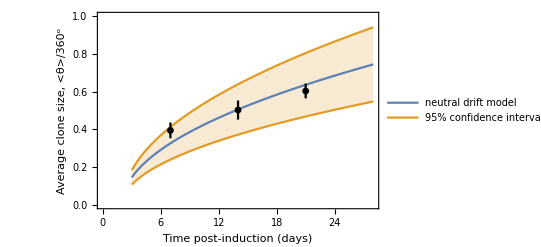

```mathematica
bands95[x_]=nlmk["MeanPredictionBands",ConfidenceLevel->.95];
Show[Plot[{nlmk[x],bands95[x]},{x,3,28},Filling->{2->{1}},PlotRange->{0,1},Frame->True,FrameStyle->{Black,Black,Black,Black},PlotStyle->Automatic,LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Time post-induction (days)","Average clone size, <θ>/360^o"},PlotLegends->{"neutral drift model","95% confidence interval"}],ErrorListPlot[avker,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,7}]]
```

```mathematica
{p1,p2,p3}={128.3657722,178.6340816,216.5464748};{per1,per2,per3}={16.04572152,15.26173956,23.08393178};
```

```mathematica
avp={{7,p1/360},{14,p2/360},{21,p3/360}}
```

{{7,0.356572},{14,0.496206},{21,0.601518}}

```mathematica
avper={{{7,p1/360},ErrorBar[per1/360]},{{14,p2/360},ErrorBar[per2/360]},{{21,p3/360},ErrorBar[per3/360]}}
```

{{{7,0.356572},ErrorBar[0.0445714]},{{14,0.496206},ErrorBar[0.0423937]},{{21,0.601518},ErrorBar[0.064122]}}

```mathematica
nlmp=NonlinearModelFit[avp,model,a,x]
```

FittedModel[0.142727 √(-2+x)]

```mathematica
p=0.14272726878440115/Sqrt[Pi];per=nlmp["ParameterErrors"]/Sqrt[Pi]
```

{0.00284337}

```mathematica
savper={{{(7-tdelay)p^2,p1/360},ErrorBar[per1/360]},{{(14-tdelay)p^2,p2/360},ErrorBar[per2/360]},{{(21-tdelay)p^2,p3/360},ErrorBar[per3/360]}};
```

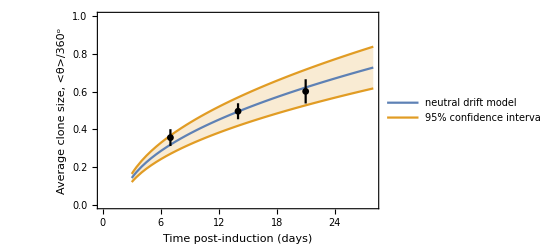

```mathematica
bands95[x_]=nlmp["MeanPredictionBands",ConfidenceLevel->.95];
Show[Plot[{nlmp[x],bands95[x]},{x,3,28},Filling->{2->{1}},PlotRange->{0,1},Frame->True,FrameStyle->{Black,Black,Black,Black},PlotStyle->Automatic,LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Time post-induction (days)","Average clone size, <θ>/360^o"},PlotLegends->{"neutral drift model","95% confidence interval"}],ErrorListPlot[avper,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,7}]]
```

```mathematica
{n1,n2,n3}={83.78547376,130.8555399,164.8091627};{ner1,ner2,ner3}={9.486836773,14.02918646,14.56720957};
```

```mathematica
avn={{7,n1/360},{14,n2/360},{21,n3/360}}
```

{{7,0.232737},{14,0.363488},{21,0.457803}}

```mathematica
nlmn=NonlinearModelFit[avn,model,a,x]
```

FittedModel[0.104864 √(-2+x)]

```mathematica
n=0.10486368728013508 /Sqrt[Pi];ner=nlmn["ParameterErrors"]/Sqrt[Pi]
```

{0.000126255}

```mathematica
avner={{{7,n1/360},ErrorBar[ner1/360]},{{14,n2/360},ErrorBar[ner2/360]},{{21,n3/360},ErrorBar[ner3/360]}};
```

```mathematica
savner={{{(7-tdelay)n^2,n1/360},ErrorBar[ner1/360]},{{(14-tdelay)n^2,n2/360},ErrorBar[ner2/360]},{{(21-tdelay)n^2,n3/360},ErrorBar[ner3/360]}};
```

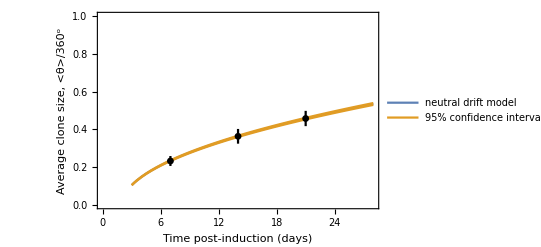

```mathematica
bands95[x_]=nlmn["MeanPredictionBands",ConfidenceLevel->.95];
Show[Plot[{nlmn[x],bands95[x]},{x,3,28},Filling->{2->{1}},PlotRange->{0,1},Frame->True,FrameStyle->{Black,Black,Black,Black},PlotStyle->Automatic,LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Time post-induction (days)","Average clone size, <θ>/360^o"},PlotLegends->{"neutral drift model","95% confidence interval"}],ErrorListPlot[avner,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,7}]]
```

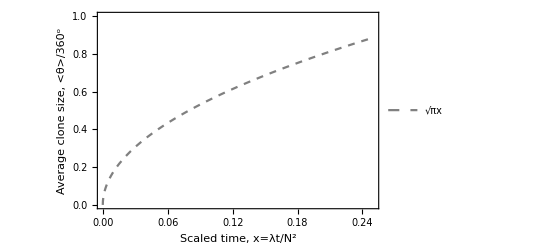

```mathematica
g2=Plot[Sqrt[Pi x],{x,0,0.25},PlotRange->{0,1},FrameStyle->{Black,Black,Black,Black},Frame->True,PlotStyle->{Dashed,Gray},LabelStyle->{FontFamily->"Myriad Pro",FontSize->16},FrameLabel->{"Scaled time, x=λt/N^2","Average clone size, <θ>/360^o"},PlotLegends->{Style["√πx",FontFamily->"Myriad Pro",FontSize->16]}]
```

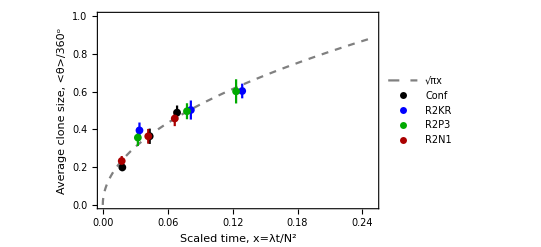

```mathematica
Show[g2,ErrorListPlot[savcnfer,PlotStyle->GrayLevel[0.0],PlotMarkers->{Automatic,8},PlotLegends->{Style["Conf",FontFamily->"Myriad Pro",FontSize->16]}],ErrorListPlot[savker,PlotStyle->Blue,PlotMarkers->{Automatic,8},PlotLegends->{Style["R2KR",FontFamily->"Myriad Pro",FontSize->16]}],ErrorListPlot[savper,PlotStyle->Darker[Green],PlotMarkers->{Automatic,8},PlotLegends->{Style["R2P3",FontFamily->"Myriad Pro",FontSize->16]}],ErrorListPlot[savner,PlotStyle->Darker[Red],PlotMarkers->{Automatic,8},PlotLegends->{Style["R2N1",FontFamily->"Myriad Pro",FontSize->16]}]]
```

```mathematica
ratios:
```

```mathematica
rWT2k={cnf/k,Sqrt[(cnfer/cnf)^2+(ker/k)^2]cnf/k}
```

{0.72993,{0.0468114}}

```mathematica
rWT2p={cnf/p,Sqrt[(cnfer/cnf)^2+(per/p)^2]cnf/p}
```

{0.746469,{0.0467962}}

```mathematica
rWT2n={cnf/n,Sqrt[(cnfer/cnf)^2+(ner/n)^2]cnf/n}
```

{1.016,{0.0526733}}